```mathematica
(*Asignación de supuestos generales*)
$Assumptions={r>0,s>0,X>0,y>0,T>0,κ>0,σ>0};
(*Definición de funciones*)
F1[X_,y_,ν_,T_]:=y^(3*ν/2)*(HankelH1[ν,X]+HankelH2[ν,X])/(2*σ+I*T/12)^(3*ν+1)
F2[X_,y_,ν_,T_]:=(κ*y^(3*ν/2)*(y-(4*σ+I*T/6)*(3*ν+1))/(2*σ+I*T/12)^(3*(ν+1)))*Sum[(-1)^p*(HankelH1[ν-1+2*p,X]+HankelH2[ν-1+2*p,X]),{p,0,1}]
(*Cálculo de constantes auxiliares*)
A=(Sqrt[π]/(2*Sqrt[r]))*(1+Erf[Sqrt[r]*s]);
B[m_]:=(r^(-(m+1)/2)/2)*((1+(-1)^m)*Gamma[(1+m)/2]+(-1)^(1+m)*Gamma[(1+m)/2,r*s^2]);
```

```mathematica
(*Definición de funciones Ψ*)
Ψ1[X_,y_,T_]:=
A*F1[X,y,s,T]+2*c1*(Derivative[0,0,1,0][F1][X,y,s,T]/1!)*B[1]+2*c12*(Derivative[0,0,2,0][F1][X,y,s,T]/2!)*B[2]+2*c13*(Derivative[0,0,3,0][F1][X,y,s,T]/3!)*B[3];
Ψ2[X_,y_,T_]:=(X/2)*A*F2[X,y,s,T]+c1*(X/2)*(Derivative[0,0,1,0][F2][X,y,s,T]/1!)*B[1]+c12*(X/2)*(Derivative[0,0,2,0][F2][X,y,s,T]/2!)*B[2]+c13*(X/2)*(Derivative[0,0,3,0][F2][X,y,s,T]/3!)*B[3];
Ψ[X_,y_,T_]:=(3/2)*(3*λ/2)^(1/6)*(X^(1/3)/y^(1/2))*Exp[-y/(4*σ+I*T/6)]*(Ψ1[X,y,T]+Ψ2[X,y,T]);
```

```mathematica
(*Modificaciones de Ψ para obtener sus módulos cuadrados*)
Mod2Ψ[X_,y_,T_]:=Re[N[Conjugate[Ψ[X,y,T]]*Ψ[X,y,T]]]
Mod2Ψ1[X_,y_,T_]:=Conjugate[Ψ1[X,y,T]]*Ψ1[X,y,T]
Mod2Ψ2[X_,y_,T_]:=Conjugate[Ψ2[X,y,T]]*Ψ2[X,y,T]
```

```mathematica
(*Normalización de Ψ y cálculo de su módulo cuadrado*)
NΨ[X_,y_,T_]:=Ψ[X,y,T]/NIntegrate[𝒳^(-5/3)*𝓎*Mod2Ψ[𝒳,𝓎,T],{𝒳,0,Infinity},{𝓎,0,Infinity},WorkingPrecision->MachinePrecision]
Mod2NΨ[X_,y_,T_]:=Re[N[Conjugate[NΨ[X,y,T]]*NΨ[X,y,T]]]//Quiet
```

```mathematica
(*Función para graficar*)
PlotFunction[xe_,ye_,T_]:=Plot3D[{ReplaceAll[Mod2Ψ[X,y,T],X->Sqrt[2/(3*λ)]*(x)^3]},{x,2,xe},{y,10,ye},PlotRange->Full,WorkingPrecision->MachinePrecision,AxesLabel->{x,y,(|Ψ|)^2},Ticks->{Automatic,Automatic,None},LabelStyle->Directive[Black,Bold],MeshStyle->Red,PlotStyle->LightBlue]//Quiet
```

```mathematica
(*Evaluación y gráficos Without Rainbow*)
λ=1;
c1=0;
c12=0;
c13=0;
s=10;
κ=N[0,$MachinePrecision];
σ=N[0.3,$MachinePrecision];
r=N[10^3,$MachinePrecision];
(*Gráficos con diferentes parámetros [X,y,T]*)
PlotFunction[3.15,40,0]
PlotFunction[3.15,100,10]
PlotFunction[3.26,650,30]
PlotFunction[3.26,1300,50]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*Evaluación y gráficos With Rainbow*)
λ=1;
c1=0;
c12=0;
c13=0;
κ=N[5*10^(-4),$MachinePrecision];
s=10;
σ=N[0.3,$MachinePrecision];
r=N[10^3,$MachinePrecision];
(*Gráficos con diferentes parámetros*)
PlotFunction[3.92,40,0]
PlotFunction[3.92,100,10]
PlotFunction[3.92,650,30]
PlotFunction[3.92,1300,50]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*Evaluación y gráficos: Without Rainbow*)
λ=1;
c1=0;
c12=0;
c13=0;
κ=N[0,$MachinePrecision];
s=10;
σ=N[0.3,$MachinePrecision];
r=N[10^3,$MachinePrecision];
(*Cálculo de valor esperado<a> y su gráfica*)α:=(3*λ/2)^(1/6);
Numerador1[T_]:=Quiet[NIntegrate[(X^(-4/3)*y^(1/2)*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Denominador1[T_]:=Quiet[NIntegrate[(X^(-5/3)*y*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Valoresperadoa1[T_]:=If[Denominador1[T]==0,0,Numerador1[T]/Denominador1[T]];
Plot1W:=Plot[Valoresperadoa1[T],{T,0,100},AxesLabel->None,Frame->True,FrameLabel->{"T","⟨a⟩(T)"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold],PlotStyle->{Blue,Thick},PlotRange->All]
(*Cálculo de valor esperado<ϕ>y su gráfica*)
Numerador2[T_]:=Quiet[NIntegrate[(X^(-5/3)*y^(2)*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Denominador2[T_]:=Quiet[NIntegrate[(X^(-5/3)*y*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Valoresperadoϕ1[T_]:=If[Denominador2[T]==0,0,Numerador2[T]/Denominador2[T]];
Plot2W:=Plot[Valoresperadoϕ1[T],{T,0,100},AxesLabel->None,Frame->True,FrameLabel->{"T","⟨ϕ⟩(T)"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold],PlotStyle->{Blue,Thick},PlotRange->All]
```

```mathematica
(*Evaluación y gráficos: With Rainbow*)
λ=1;
c1=0;
c12=0;
c13=0;
κ=N[5*10^(-2),$MachinePrecision];
s=10;
σ=N[0.3,$MachinePrecision];
r=N[10^3,$MachinePrecision];
(*Cálculo de valor esperado<a>y su gráfica*)α:=(3*λ/2)^(1/6);
Numerador3[T_]:=Quiet[NIntegrate[(X^(-4/3)*y^(1/2)*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Denominador3[T_]:=Quiet[NIntegrate[(X^(-5/3)*y*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Valoresperadoa2[T_]:=If[Denominador3[T]==0,0,Numerador3[T]/Denominador3[T]];
Plot3R:=Plot[Valoresperadoa2[T],{T,0,100},AxesLabel->None,Frame->True,FrameLabel->{"T","⟨a⟩(T)"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold],PlotStyle->{Red,Thick},PlotRange->All]
(*Cálculo de valor esperado<ϕ>y su gráfica*)
Numerador4[T_]:=Quiet[NIntegrate[(X^(-5/3)*y^(2)*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Denominador4[T_]:=Quiet[NIntegrate[(X^(-5/3)*y*Mod2Ψ[X,y,T]),{X,0,1000},{y,0,1000},Method->"GlobalAdaptive",WorkingPrecision->MachinePrecision]];
Valoresperadoϕ2[T_]:=If[Denominador4[T]==0,0,Numerador4[T]/Denominador4[T]];
Plot4R:=Plot[Valoresperadoϕ2[T],{T,0,100},AxesLabel->None,Frame->True,FrameLabel->{"T","⟨ϕ⟩(T)"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold],PlotStyle->{Red,Thick},PlotRange->All]
```

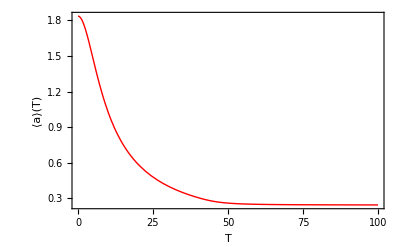

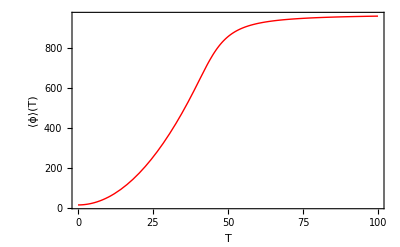

```mathematica
Plot3R
Plot4R
Show[Plot1W,Plot3R]
Show[Plot2W,Plot4R]
Plot1W
Plot2W
```